## Magnon dispersion relation

```mathematica
(*** (23.67), (23.85), (23.98), and (23.102) in my notes ***)
disp={xp/xm==E^(I p),xp+1/xp==(u+I/2)/h,xm+1/xm==(u-I/2)/h,x+1/x==u/h,xp==I d/b,xm==-I a/c,a d-b c==1,a d+b c==H,K==a b,Kbar==c d};


(*** express all variables in terms of x ***)
xsub=Solve[disp,{H,b,c,d,K,Kbar,p,xp,xm,u}][[2]]/.{C[1]->0}//Simplify;

(*** express all variables in terms of u ***)
usub=Solve[disp,{H,b,c,d,K,Kbar,p,xp,xm,x}][[1]]/.{C[1]->0}//Simplify;

(*** verifying (23.68) and (23.85) ***)
xp+1/xp-xm-1/xm==I/h/.xsub//FullSimplify
H==-1-2I h(xp-xm)==1+2I h (1/xp-1/xm)/.xsub//FullSimplify
H^2==1+4 K Kbar==1+16 h^2 Sin[p/2]^2/.xsub//FullSimplify
```

True

True

True

```mathematica
(*** strong coupling expansion of xp, xm in terms of x, as in (23.103) ***)
xpmStrong=Assuming[h>0 && x>1,Series[{xp,xm}/.xsub,{h,Infinity,4}]//Simplify]
```

{x+(ⅈ x^2)/(2 (-1+x^2) h)+x^3/(4 (-1+x^2)^3 h^2)-(ⅈ x^4 (1+x^2))/(8 (-1+x^2)^5 h^3)-(x^5 (1+3 x^2+x^4))/(16 (-1+x^2)^7 h^4)+O[1/h]^5,x+(ⅈ x^2)/((2-2 x^2) h)+x^3/(4 (-1+x^2)^3 h^2)+(ⅈ x^4 (1+x^2))/(8 (-1+x^2)^5 h^3)-(x^5 (1+3 x^2+x^4))/(16 (-1+x^2)^7 h^4)+O[1/h]^5}

```mathematica
(*** weak coupling expansion of xp, xm, p, H in terms of u, as in (24.79) ***)
xpmWeak=Assuming[h>0 && u<0,Series[{xp,xm}/.usub,{h,0,4}]//Simplify]
Assuming[h>0 && u<0,Series[{p,H}/.usub,{h,0,4}]//Simplify]
```

{(ⅈ/2+u)/h-(2 h)/(ⅈ+2 u)-(8 h^3)/(ⅈ+2 u)^3+O[h]^5,(-ⅈ/2+u)/h+(2 h)/(ⅈ-2 u)+(8 h^3)/(ⅈ-2 u)^3+O[h]^5}

{-ⅈ Log[(ⅈ+2 u)/(-ⅈ+2 u)]+(32 u h^2)/((1+4 u^2)^2)+(384 u (-1+4 u^2) h^4)/((1+4 u^2)^4)+O[h]^5,1+(8 h^2)/(1+4 u^2)+(32 (-1+12 u^2) h^4)/((1+4 u^2)^3)+O[h]^5}

## S-matrix of the su(2|2) spin chain

```mathematica
(*** su(2|2) S-matrix elements as in (23.86) ***)

A12=S[1,2] (xp[2]-xm[1])/(xm[2]-xp[1]);
B12=S[1,2] (xp[2]-xm[1])/(xm[2]-xp[1]) (1-2 (xp[2]-xp[1])/(xp[2]-xm[1]) (xm[2]-1/xp[1])/(xm[2]-1/xm[1]));
C12=S[1,2] 2/h a[1] a[2]/(xm[1] xm[2]-1) (xp[2]-xp[1])/(xm[2]-xp[1]);
D12=-S[1,2];
E12=-S[1,2] (1-2 (xm[2]-xm[1])/(xm[2]-xp[1]) (xp[2]-1/xm[1])/(xp[2]-1/xp[1]));
F12=-S[1,2] 2 h/(a[1] a[2]) (xp[1]-xm[1]) (xp[2]-xm[2])/(xp[1] xp[2]-1) (xm[2]-xm[1])/(xm[2]-xp[1]);
G12=S[1,2](xp[2]-xp[1])/(xm[2]-xp[1]);
H12=S[1,2] a[1]/a[2] (xp[2]-xm[2])/(xm[2]-xp[1]);
K12=S[1,2] a[2]/a[1] (xp[1]-xm[1])/(xm[2]-xp[1]);
L12=S[1,2] (xm[2]-xm[1])/(xm[2]-xp[1]);

(*** the 2-body S-matrix, with S12 (23.87) factored out ***)
SmatBosonic=1/S[1,2]*{{(D12-E12)/2,(D12+E12)/2,-F12/2,F12/2},{(D12+E12)/2,(D12-E12)/2,F12/2,-F12/2},{-C12/2,C12/2,(A12-B12)/2,(A12+B12)/2},{C12/2,-C12/2,(A12+B12)/2,(A12-B12)/2}};
SmatFermionic=1/S[1,2]*{{H12,G12},{L12,K12}};

WeakSub=Flatten[Table[{xp[i]->#[[1]],xm[i]->#[[2]]} & [Evaluate[xpmWeak/.u->u[i]]],{i,1,2}]];
StrongSub=Flatten[Table[{xp[i]->#[[1]],xm[i]->#[[2]]} & [Evaluate[xpmStrong/.x->x[i]]],{i,1,2}]];

swap={f_[1]->f[2],f_[2]->f[1],S[1,2]->S[2,1]};

(*** checking (23.83) ***)
A12==a[1]/a[2]*K12+G12==L12+a[2]/a[1]*H12//Simplify
```

True

```mathematica
(*** checking unitarity relation S(2,1)=S(1,2)^-1 in the weak and strong coupling expansion ***)
((SmatBosonic/.swap)-Inverse[SmatBosonic])/.WeakSub//Simplify
((SmatBosonic/.swap)-Inverse[SmatBosonic])/.StrongSub//Simplify

((SmatFermionic/.swap)-Inverse[SmatFermionic])/.WeakSub//Simplify
((SmatFermionic/.swap)-Inverse[SmatFermionic])/.StrongSub//Simplify
```

{{O[h]^6,O[h]^6,O[h]^7,O[h]^7},{O[h]^6,O[h]^6,O[h]^7,O[h]^7},{O[h]^7,O[h]^7,O[h]^6,O[h]^6},{O[h]^7,O[h]^7,O[h]^6,O[h]^6}}

{{O[1/h]^5,O[1/h]^5,O[1/h]^4,O[1/h]^4},{O[1/h]^5,O[1/h]^5,O[1/h]^4,O[1/h]^4},{O[1/h]^6,O[1/h]^6,O[1/h]^5,O[1/h]^5},{O[1/h]^6,O[1/h]^6,O[1/h]^5,O[1/h]^5}}

{{O[h]^6,O[h]^6},{O[h]^6,O[h]^6}}

{{O[1/h]^5,O[1/h]^5},{O[1/h]^5,O[1/h]^5}}

## Level II S-matrix

```mathematica
(*** level II wave function and II,I scattering phase as in (23.153) ***)
levelIIsub={f[i_]:>a[i]/(y-xp[i]),SII[i_]:>(y-xm[i])/(y-xp[i])};

(*** verifying (23.152) ***)
{f[1] L12+f[2] SII[1] H12==A12 f[1] SII[2],f[1] K12+f[2] SII[1] G12==A12 f[2]}/.levelIIsub//Simplify
```

{True,True}

## Crossing transformation

```mathematica
(*** (23.92) ***)
S[2,1]=1/S[1,2];

(*** dressing phase as defined in (23.87) ***)
Stoσ={S[i_,j_]->Sqrt[(xm[j]-xp[i])/(xp[j]-xm[i])*(1-1/(xp[j] xm[i]))/(1-1/(xm[j] xp[i]))] σ[i,j]};

(*** checking (23.177) and (23.179) ***)
{A12^2,D12^2}/.Stoσ
```

{((1-1/(xm[1] xp[2])) (-xm[1]+xp[2]) σ[1,2]^2)/((1-1/(xm[2] xp[1])) (xm[2]-xp[1])),((xm[2]-xp[1]) (1-1/(xm[1] xp[2])) σ[1,2]^2)/((1-1/(xm[2] xp[1])) (-xm[1]+xp[2]))}

```mathematica
(*** crossing transformation as in (23.93) ***)
crossing={xp[1]->xp[-1],xm[1]->xm[-1],S[1,2]->S[-1,2]};
xp[-1]:=1/xp[1];
xm[-1]:=1/xm[1];

(*** crossing condition as in (23.96), to be set to 1 ***)
CrossingRatioS=(L12/.crossing)/(G12/.swap)//Simplify
CrossingRatioσ=CrossingRatioS/.Stoσ//Simplify
```

(S[-1,2] S[1,2] (-1/xm[1]+xm[2]) xp[1] (xm[1]-xp[2]))/((-1+xm[2] xp[1]) (xp[1]-xp[2]))

((-1/xm[1]+xm[2]) xp[1] (xm[1]-xp[2]) √((xm[2] (xm[2]-xp[1]) xp[1] (1-1/(xm[1] xp[2])))/((-1+xm[2] xp[1]) (-xm[1]+xp[2]))) √((xm[1] xm[2] (xm[2]-1/xp[1]) (1-xm[1]/xp[2]))/((xm[2]-xp[1]) (-1+xm[1] xp[2]))) σ[-1,2] σ[1,2])/((-1+xm[2] xp[1]) (xp[1]-xp[2]))

```mathematica
(*** checking (23.97) ***)
σσphase=(xp[2]/xm[2])*(xp[2]-xp[1])/(xp[2]-xm[1])*(xm[2]-1/xp[1])/(xm[2]-1/xm[1]);
σcross={σ[-1,2]->σσphase/σ[1,2]};

branchassumption=(xm[2]>xp[1]>1 && xp[2]>xm[1]>1 );
Assuming[branchassumption,(CrossingRatioσ/.σcross)==1//Simplify]
```

True

## Checking crossing symmetry at strong coupling

```mathematica
(*** the leading strong coupling expression for the function χ (23.105) ***)
χ0[x_,y_]=Sum[h/((r-1)(s-1))(1/(x^(r-1) y^(s-1))-1/(x^(s-1) y^(r-1)))/.{s->r+1},{r,2,Infinity}]//FullSimplify

θ0=χ0[xp[1],xp[2]]+χ0[xm[1],xm[2]]-χ0[xp[1],xm[2]]-χ0[xm[1],xp[2]];

(*** agreement at order h^-1 as in (23.104) ***)
Series[θ0+(θ0/.crossing)/.StrongSub,{h,Infinity,2}]//Simplify
Series[-I Log[σσphase]/.StrongSub,{h,Infinity,2}]//Simplify
```

(h (x-y) (1+(-1+x y) Log[1-1/(x y)]))/(x y)

(x[2] (-2 x[1]+x[2]+x[1]^2 x[2]))/((x[1]-x[2]) (-1+x[1] x[2]) (-1+x[2]^2) h)+O[1/h]^3

(x[2] (-2 x[1]+x[2]+x[1]^2 x[2]))/((x[1]-x[2]) (-1+x[1] x[2]) (-1+x[2]^2) h)+(ⅈ x[1]^2 x[2]^2 (1-4 x[1] x[2]+x[2]^2+x[1]^2 (1+x[2]^2)))/(2 (-1+x[1]^2) (x[1]-x[2])^2 (-1+x[1] x[2])^2 (-1+x[2]^2) h^2)+O[1/h]^3

## The all-order dressing phase

```mathematica
(*** the function χ in (23.101) ***)
χ[x_,y_,h_,rsorder_]:=Sum[crs[r,s,h]/((r-1)(s-1))(1/(x^(r-1) y^(s-1))-1/(x^(s-1) y^(r-1))),{r,2,rsorder},{s,r+1,rsorder,2}]

(*** coefficient Subscript[c, r,s](h) in the strong coupling expansion (23.107) ***)
cStrong[r_,s_,n_]:=Zeta[n]/((-2Pi)^n Gamma[n-1]) * (r-1)(s-1) Gamma[(s+r+n-3)/2]Gamma[(s-r+n-1)/2]/(Gamma[(s+r-n+1)/2] Gamma[(s-r-n+3)/2])/;n>=2
cStrong[r_,s_,1]:=-2/Pi (r-1)(s-1)/((s+r-2)(s-r))
cStrong[r_,s_,0]:=KroneckerDelta[s,r+1]

crsStrong[r_,s_,h_,horder_]:=Sum[cStrong[r,s,n] h^(1-n),{n,0,horder}]

(*** coefficient Subscript[c, r,s](h) in the weak coupling expansion (23.108) ***)
cWeak[r_,s_,n_]:=2 Cos[Pi n/2] (-1)^(n+s) Zeta[n+1] Gamma[n+2] Gamma[n+1] (r-1)(s-1)/(Gamma[(n-r-s+5)/2] Gamma[(n+r-s+3)/2]Gamma[(n-r+s+3)/2]Gamma[(n+r+s+1)/2])

crsWeak[r_,s_,h_,horder_]:=Sum[cWeak[r,s,n] h^(n+1),{n,r+s-3,horder}]

θ[h_,rsorder_]:=χ[xp[1],xp[2],h,rsorder]+χ[xm[1],xm[2],h,rsorder]-χ[xp[1],xm[2],h,rsorder]-χ[xm[1],xp[2],h,rsorder];

(*** DHM representation of χ[x,y], valid for |x|,|y|>1, as in (23.106) ***)
DHM[x_,y_,h_]:=NIntegrate[(-I (I z1) (I z2)/((2Pi I)^2 (z1-x)(z2-y)) (LogGamma[1+I h(z1+1/z1-z2-1/z2)]-LogGamma[1-I h (z1+1/z1-z2-1/z2)])/.{z1->E^(I θ1),z2->E^(I θ2)}),{θ1,0,2Pi},{θ2,0,2Pi}]
```

```mathematica
(*** check χ0, θ0 as the strong coupling limit expressions ***)
(χ[x,y,h,Infinity]/.crs[f___]:>crsStrong[f,0])-χ0[x,y]==0//Simplify
(θ[h,Infinity]/.crs[f___]:>crsStrong[f,0])-θ0==0//Simplify


(*** testing DHM representation at strong coupling, with increasing truncation order ***)
{χ[4.3,2.1,3.3,15]/.crs[f___]:>crsStrong[f,3],
χ[4.3,2.1,3.3,15]/.crs[f___]:>crsStrong[f,5],
χ[4.3,2.1,3.3,15]/.crs[f___]:>crsStrong[f,10],
DHM[4.3,2.1,3.3]}

(*** testing DHM representation at weak coupling, with increasing truncation order ***)
{χ[4.3,2.1,.1,5]/.crs[f___]:>crsWeak[f,5],
χ[4.3,2.1,.1,10]/.crs[f___]:>crsWeak[f,10],
χ[4.3,2.1,.1,25]/.crs[f___]:>crsWeak[f,20],
DHM[4.3,2.1,.1]}
```

True

True

{0.0401025,0.0401081,0.0401084,0.0401084+3.05609×10^-18 ⅈ}

{0.0000591733,0.0000597088,0.0000597079,0.0000597079-7.45389×10^-19 ⅈ}

## Analytic continuation of the DHM representation

```mathematica
(*** analytic continuation of the DHM representation outside of the region |x|>1, |y|>1, as in Arutyunov-Frolov, arXiv:0904.4575, with an overall sign difference in convention ***)

AFΨ[x_,y_,h_]:=NIntegrate[(-I (I z2)/((2Pi I) (z2-y)) (LogGamma[1+I h(x+1/x-z2-1/z2)]-LogGamma[1-I h (x+1/x-z2-1/z2)])/.{z2->E^(I θ2)}),{θ2,0,2Pi}]
DHMcrossx[x_,y_,h_]:=DHM[x,y,h]-AFΨ[x,y,h]
DHMcrossy[x_,y_,h_]:=DHM[x,y,h]+AFΨ[y,x,h]
DHMcrossxy[x_,y_,h_]:=DHM[x,y,h]-AFΨ[x,y,h]+AFΨ[y,x,h]-I (LogGamma[1+I h(x+1/x-y-1/y)]-LogGamma[1-I h (x+1/x-y-1/y)])

x12sub[u_,v_,h_]=Flatten[Table[{xp[i]->#[[1]],xm[i]->#[[2]]} & [Evaluate[({xp,xm}/.xsub)/.x->x[i]]],{i,1,2}]]/.{x[1]->u,x[2]->v};

χanalytic[x_,y_,h_]:=DHM[x,y,h]/;(Abs[x]>1 && Abs[y]>1)
χanalytic[x_,y_,h_]:=DHMcrossx[x,y,h]/;(Abs[x]<1 && Abs[y]>1)
χanalytic[x_,y_,h_]:=DHMcrossy[x,y,h]/;(Abs[x]>1 && Abs[y]<1)
χanalytic[x_,y_,h_]:=DHMcrossxy[x,y,h]/;(Abs[x]<1 && Abs[y]<1)

θanalytic[x_,y_,h_]:=χanalytic[xp[1],xp[2],h]+χanalytic[xm[1],xm[2],h]-χanalytic[xp[1],xm[2],h]-χanalytic[xm[1],xp[2],h]/.x12sub[x,y,h]
θcrossanalytic[x_,y_,h_]:=χanalytic[xp[-1],xp[2],h]+χanalytic[xm[-1],xm[2],h]-χanalytic[xp[-1],xm[2],h]-χanalytic[xm[-1],xp[2],h]/.x12sub[x,y,h]
```

```mathematica
(*** testing continuity across |x|=1 for |y|>1 ***)
DHM[1.001,2.1,3.3]
DHM[.999,2.1,3.3]
DHMcrossx[.999,2.1,3.3]
```

-0.399963+3.67228×10^-13 ⅈ

4.45626-8.97873×10^-12 ⅈ

-0.402331-1.88905×10^-12 ⅈ

```mathematica
(*** testing continuity across |y|=1 for |x|>1 ***)
DHM[2.1,1.001,3.3]
DHM[2.1,.999,3.3]
DHMcrossy[2.1,.999,3.3]
```

0.399963-3.68258×10^-13 ⅈ

-4.45626+8.9788×10^-12 ⅈ

0.402331+1.88912×10^-12 ⅈ

```mathematica
(*** testing continuity across |y|=1 for |x|<1 ***)
DHMcrossx[.9,1.001,3.3]
DHMcrossx[.9,.999,3.3]
DHMcrossxy[.9,.999,3.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.242961-1.98313×10^-12 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-9.32639-2.89177×10^-11 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.239275-2.89167×10^-11 ⅈ

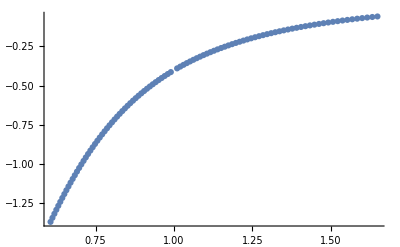

```mathematica
(*** checking that DHM and DHMcrossx smoothly join across |x|=1 in the case y=2.1 and h=3.3 ***)
dhmplot=ListPlot[Table[{E^x,DHM[E^x,2.1,3.3]//Re},{x,0.01,.5,.01}]];
dhmcrossplot=ListPlot[Table[{E^x,DHMcrossx[E^x,2.1,3.3]//Re},{x,-.5,-0.01,.01}]];
Show[{dhmplot,dhmcrossplot},PlotRange->All]
```

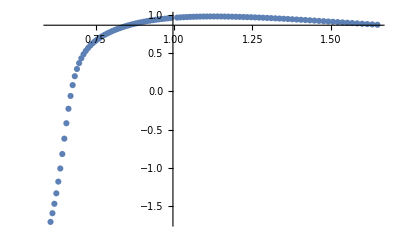

```mathematica
(*** checking that DHMcrossx and DHMcrossxy smoothly join across |x|=1 in the case y=.8 and h=3.3 ***)
dhmplot=ListPlot[Table[{E^x,DHMcrossy[E^(x+.3 I),.8,3.3]//Re},{x,0.01,.5,.01}]];
dhmcrossplot=ListPlot[Table[{E^x,DHMcrossxy[E^(x+.3 I),.8,3.3]//Re},{x,-.5,-0.01,.01}]];
Show[{dhmplot,dhmcrossplot},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

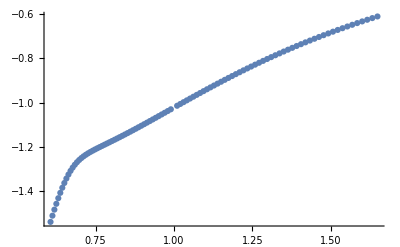

```mathematica
(*** still works for complex y close to |y|=1 ***)
dhmplot=ListPlot[Table[{E^x,DHMcrossy[E^(x+.3 I),.6+.6 I,3.3]//Re},{x,0.01,.5,.01}]];
dhmcrossplot=ListPlot[Table[{E^x,DHMcrossxy[E^(x+.3 I),.6+.6 I,3.3]//Re},{x,-.5,-0.01,.01}]];
Show[{dhmplot,dhmcrossplot},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 5.63115-2.32506 ⅈ and 0.00206998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 5.53724-2.35477 ⅈ and 0.00209426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 5.44829-2.37753 ⅈ and 0.00150669 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 8.37804-4.29326 ⅈ and 0.00129065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 8.35154-4.28506 ⅈ and 0.00129623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ2 near {θ2} = {0.723941}. NIntegrate obtained 8.3252-4.27679 ⅈ and 0.00130184 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

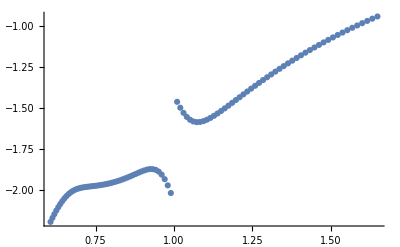

{1.17132,0.922623}

```mathematica
(*** Warning: formula for the analytic continuation fails when y is too far from the unit circle! ***)
dhmplot=ListPlot[Table[{E^x,DHMcrossy[E^(x+.3 I),.5+.5 I,3.3]//Re},{x,0.01,.5,.01}]];
dhmcrossplot=ListPlot[Table[{E^x,DHMcrossxy[E^(x+.3 I),.5+.5 I,3.3]//Re},{x,-.5,-0.01,.01}]];
Show[{dhmplot,dhmcrossplot},PlotRange->All]
```

## Numerical test of crossing

```mathematica
(*** for x=0.75-0.6i and h=3.3, x^+ and x^- are not far from the unit circle, where the simple analytically continued formulae of the dressing phase will be valid ***)
{xp,xm}/.xsub/.h->3.3/.x->.75-.6I//Abs
```

{1.17132,0.922623}

```mathematica
(*** checking crossing for x=0.75-0.6i, y=1.2, and h=3.3, it works! ***)
θanalytic[.75-.6I,1.2,3.3]+θcrossanalytic[.75-.6I,1.2,3.3]
-I Log[σσphase]/.x12sub[.75-.6I,1.2,3.3]
```

-0.224894-0.0600977 ⅈ

-0.224894-0.0600977 ⅈ